### Tools

```mathematica
ClearAll["Global`*"]
Needs["BenderWu`"]
SetDirectory[NotebookDirectory[]];

(*Potential*)
m[z_,e_]:=4 z e/(1+(z+e)^2);
V[x_, z_, e_]:=JacobiSN[x,m[z,e]]^2 (1+(z-e)^2 JacobiSN[x,m[z,e]]^2)/JacobiDN[x,m[z,e]]^2
(*For numeric computations, the using the potential as an expansion in x incrases speed.*)
VSeries[x_,z_,e_,N_]:=Series[V[x, z, e],{x,0,N}]//Normal

(*Some machinery*)
MyBW[zin_,ein_,nu_,order_]:=BenderWu[Evaluate[V[x, zin, ein]]/.z->zin/.e->ein,x,nu,order,Monitor->False]
MyBWNumeric[z_,e_,nu_,order_]:=BenderWu[VSeries[x,z,e,2 order+2],x,nu,order]

(*Compute the series with some normalisation*)
MyBWSeries[BW_]:=Collect[Sqrt[2] BWProcess[BW,OutputStyle->"Series",Coupling->2^(1/4) g],g]
```

```mathematica
(*Main function used to compute perturbative series and Pade poles*)
Main=Function[{Deformations, Order, FileName},

StartTime=AbsoluteTime[];
DeformationProbes=Deformations;
k=Order;

(*Let's create some large amount of numeric data*)
DeformationProbesP=SetPrecision[DeformationProbes, 4k];
Do[Monitor[
FctData[i]=MyBWNumeric[DeformationProbesP[[i,1]], DeformationProbesP[[i,2]],0, k];
PertData[i]=MyBWSeries[FctData[i]],
"Performing Bender-Wu Perturbative Data: " <>ToString[i]<>"/"<>ToString[Length[DeformationProbes]]]
, {i, 1, Length[DeformationProbes]}];


(*Save the data to some file*)
SetDirectory[NotebookDirectory[]];
ExportFile= "Data/"<>FileName<>".m";
(*A header*)
Outstring="This data was created with the following parameters:";
Export[ExportFile, Outstring];
Save[ExportFile, k];
Save[ExportFile, DeformationProbes];
(*Export the perturbative data*)
Save[ExportFile, PertData];

(*Add Pade poles*)
Do[Monitor[
BorelTransform[i]=Sum[SeriesCoefficient[PertData[i]/. g-> Sqrt[s], {s, 0, n-1}]s^(n-1)/n!, {n, 1, k+1}];
Pade[i]=PadeApproximant[BorelTransform[i] , {s, 0, {k/2, k/2}}];
sϕ[i]=NSolve[Denominator[Pade[i]]==0, WorkingPrecision->2k];
PadePoles[i]=Table[s /. sϕ[i][[j]],{j, 1, Dimensions[sϕ[i]][[1]]}];
Save[ExportFile, PadePoles],
"Computing Pade Poles: " <>ToString[i]<>"/"<>ToString[Length[DeformationProbes]]]
, {i, 1, Length[DeformationProbes]}];

EndTime=AbsoluteTime[];
Print["The computation took " <>ToString[UnitConvert[Quantity[EndTime-StartTime,"Seconds"],MixedUnit[{"Minutes", "Seconds"}]]]<>" and ended on " <> DateString[EndTime]]
];
```

### Usage

```mathematica
(*Write Main[{{Subscript[ζ, 1], Subscript[η, 1]}, ...,{Subscript[ζ, n], Subscript[η, n]}}, k, Filename] to compute the perturbative series at {Subscript[ζ, i], Subscript[η, i]} to k^th order and save the data to Data/FileName.m*)
Main[{{0.2,0.4}, {0.3,0.4}, {0.4,0.4}}, 20, "TempData"]
```

The computation took 0.00159 hours (5.74 seconds) and ended on Wed 9 Oct 2019 10:51:00

### Work in terms of the difference and sum of η and ζ

```mathematica
constantsum=Table[{0.6, 0.2*k}, {k, -2, 6}];
constantdif=Table[{0.2*k, 0.4}, {k, -2, 6}];
zerosum=Table[{0,0.2*k}, {k, -4, 4}];
zerodif=Table[{0.2*k, 0}, {k, -4, 4}];
rotdif=Table[{0.8, 0.4*E^(I k Pi/8)}, {k, 0, 16}];
rotsum=Table[{0.8*E^(I k Pi/8),0.4}, {k, 0, 16}];
critrotsum=Table[{0.8*E^(I k Pi/8),0}, {k, 0, 16}];

AltCoords=Function[Coordinates, Module[{sum, difference, ζ, η},
sum=Coordinates[[1]];
difference=Coordinates[[2]];
ζ=(sum+difference)/2;
η=(sum-difference)/2;
{ζ,η}]];
ListAltCoords[list_]:=Table[AltCoords[list[[i]]], {i, 1, Length[list]}]

constantdif=ListAltCoords[constantdif];
constantsum=ListAltCoords[constantsum];
zerodif=ListAltCoords[zerodif];
zerosum=ListAltCoords[zerosum];
rotdif=ListAltCoords[rotdif];
rotsum=ListAltCoords[rotsum];
critrotsum=ListAltCoords[critrotsum];
```

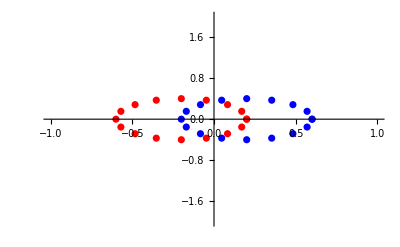

```mathematica
CplxListPlot[list_, colour_:Blue]:=ListPlot[Table[{Re[list[[i]]], Im[list[[i]]]}, {i, 1, Length[list]}], PlotStyle->colour, PlotRange->{{-1,1},{-2,2}}]
plt[points_]:=Show[CplxListPlot[Transpose[points][[1]], Blue], CplxListPlot[Transpose[points][[2]], Red]]
plt[rotsum]
```

```mathematica
kt=200
```

200

```mathematica
Main[constantsum, kt, "constantsum"]
Main[constantdif, kt, "constantdif"]
Main[zerodif, kt, "zerodif"]
Main[zerosum, kt, "zerosum"]
Main[rotdif, kt, "rotdif"]
Main[rotsum, kt, "rotsum"]
Main[critrotsum, kt, "critrotsum"]
```

The computation took 55 minutes 55.4142610 seconds and ended on Wed 9 Oct 2019 18:25:11

The computation took 50 minutes 29.8176762 seconds and ended on Wed 9 Oct 2019 19:15:41

The computation took 55 minutes 50.0059085 seconds and ended on Wed 9 Oct 2019 20:11:31

The computation took 55 minutes 50.8667022 seconds and ended on Wed 9 Oct 2019 21:07:22

The computation took 123 minutes 41.7867826 seconds and ended on Wed 9 Oct 2019 23:11:04

The computation took 132 minutes 11.5394788 seconds and ended on Thu 10 Oct 2019 01:23:15

The computation took 132 minutes 51.6974160 seconds and ended on Thu 10 Oct 2019 03:36:07

### Time Estimation

{{10,0.453125},{20,1.01563},{30,2.625},{40,5.25},{50,9.32813}}

FittedModel[0.0305235 x+2.02922×10^-6 x^2+0.0000624785 x^3]

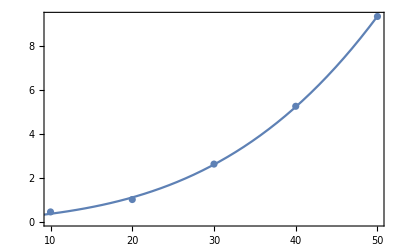

{{x→-100.563-175.558 ⅈ},{x→-100.563+175.558 ⅈ},{x→201.093}}

```mathematica
(*Let's estimate how long computations take*)
DeformationProbes={{0.2, 0.4}, {0.35, 0.4}, {0.38, 0.4}, {0.39, 0.4}, {0.395, 0.4}, {0.4, 0.4}, {0.41, 0.4}};
zin=0.38`40;
ein=0.4`40;
ttest[n_]:=Timing[BW=MyBWNumeric[zin,ein,0,n]][[1]]
end=50;
data=Table[{n, ttest[n]}, {n, 10, end, 10}]

lm=NonlinearModelFit[data,a1 x+a2 x^2+a3 x^3 , {a0, a1, a2, a3, a4}, x]
Show[ListPlot[data],Plot[lm[x],{x,0,end}],Frame->True]

NSolve[Normal[lm]==3600/7, x]
```

### Check

```mathematica
(*The numeric computations using the power series of V agree with the "exact" ones:*)
zin=0.38`40;
ein=0.4`40;
a=MyBWSeries[MyBWNumeric[zin,ein,0,4]]
b=MyBWSeries[MyBW[zin, ein, 0, 4]]
a-b
```